1.1.2 Лабораторная работа №5 
Тригонометрическая интерполяция (нечетная функция)

n - степень тригонометрического полинома
p - точка, от которой считается полином

```mathematica
interpolationOdd[fun_,n_,point_]:=Module[{n2=2(n+1),L=2Pi,xm,ym,bnk,bk,res,p=point},
xm=Table[(-L*m)/n2+L/(2n2),{m,1,n2}];
ym=N[fun/@xm];
bk=Table[2/(n+1)∑_(m=1)^(n+1) (ym[[m]]*Sin[((2π*k*xm[[m]])/L)]),{k,1,n}];
bnk=1/(n+1)∑_(m=1)^n ym[[m]]*(-1)^m;
res=(bnk+∑_(k=1)^n bk[[k]]*Sin[k*(2π)/L*p]);res

]
```

Пример 1

```mathematica
points1={2Pi,Pi/2,3.8π,4.3π, 2.5π,0.2Pi,1.3Pi};
```

```mathematica
interpolationOdd[Sin,5,x]
```

0.0431365+1. Sin[x]+9.25186×10^-18 Sin[2 x]-1.85037×10^-17 Sin[3 x]+1.85037×10^-17 Sin[4 x]-5.55112×10^-17 Sin[5 x]

```mathematica
interpolationOdd[Sin,5,#]&/@points1
```

{0.0431365,1.04314,-0.544649,0.852154,1.04314,0.630922,-0.76588}

```mathematica
new=interpolationOdd[Sin,10,#]&/@points1;
pointf=Sin/@points1; l1={points1,new}//Transpose;  l2={points1,pointf}//Transpose;
```

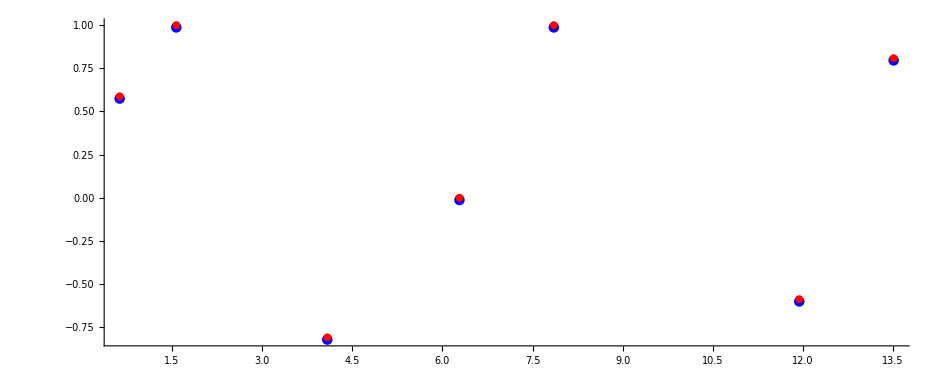

```mathematica
Show[Graphics[{Blue, PointSize[0.008],Point/@l1,Red,PointSize[0.006],Point/@l2},Axes->True]]
```

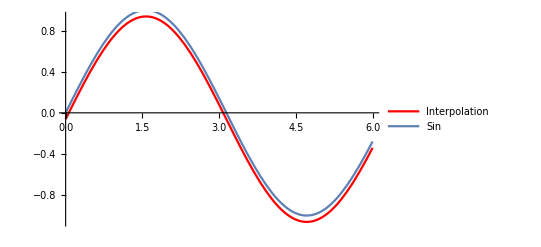

```mathematica
Show[Plot[interpolationOdd[Sin,4,k],{k,0,6},PlotStyle->Red,PlotLegends->{"Interpolation"}],Plot[Sin[k],{k,0,6},PlotLegends->{"Sin"}]]
```